```mathematica
Lz=19;
```

```mathematica
TabFibonacci=Import["LDOSFermiArcReal_161619_Rational_3D_Up+6_Dn+4.dat"];
```

```mathematica
Clear[rng,P1]
```

```mathematica
rngOld={0,Max[#]}&@(TabFibonacci[[All,3]])
```

{0,0.0146963}

```mathematica
rng = {0,0.0148}
```

{0,0.0148}

```mathematica
rng[[2]]
```

0.0148

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.0"},{rng[[2]]/2,"7.4"},{rng[[2]]-0.2*10^-3,"14.8"}}]
```

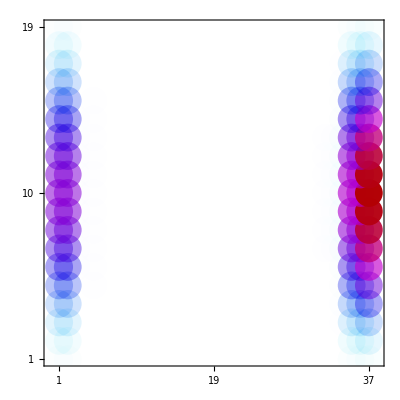

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
Frame->True,FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
BaseStyle-> 18,
PlotRange-> {{0,37+1},{1,Lz}}],
FrameTicks->{{{1,Ceiling[Lz/2],Lz},None},{{1,19,37},None}},RotateLabel-> False,
AspectRatio->1
]
```